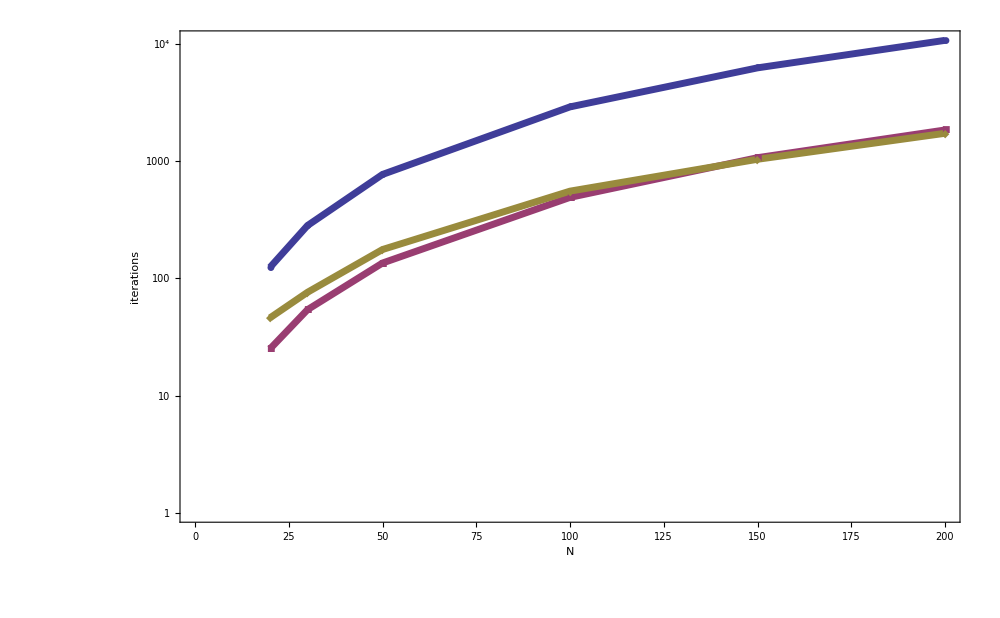

```mathematica
(*1_1*)
NN={20,30,50,100, 150, 200};
(*NN=10.^-#&/@NN;*)

sp={124,282,769,2899,6240, 10713};
spopress={46,76,176,554,1036, 1726};
spcond={25,54,135,490, 1069, 1842};
Needs["PlotLegends`"]
gp[NN_,arr_]:=Partition[Riffle[NN,arr],2];
g1=ListLogPlot[{gp[NN, sp],gp[NN,spcond], gp[NN,spopress]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegendStyle->{Large},PlotLegend->{Style["SP",20,Bold],Style["SP PRECOND",20,Bold], Style["SP OPRESS",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","iterations"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->1000]
(*Export["/home/geldor/num_ex_1_1.pdf",g1]*)
```

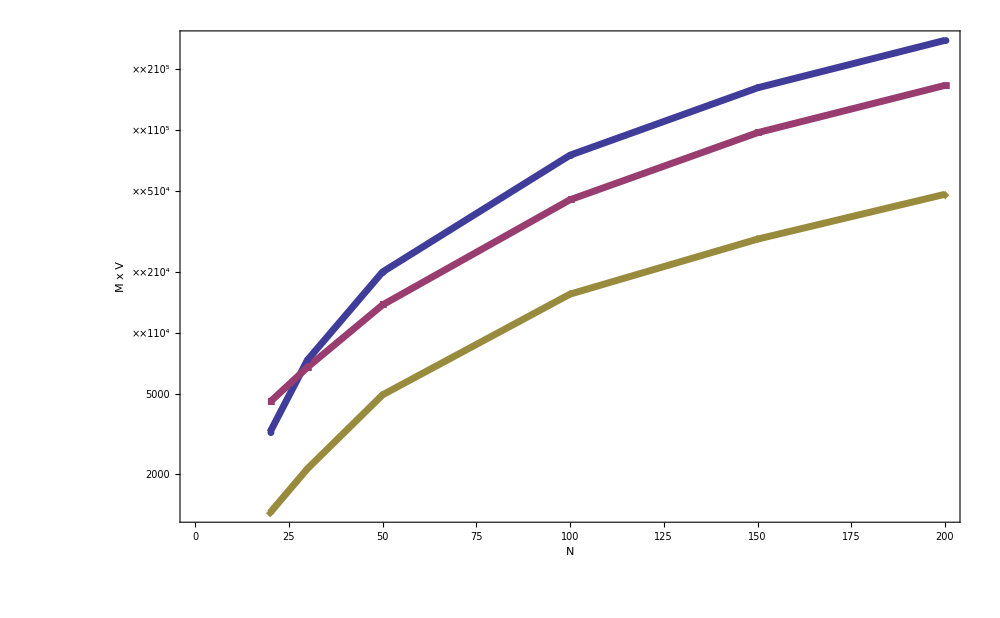

```mathematica
sp={3225,7333,19955,75375,162241, 278539};
spopress={1289,2129,4929,15513,29009, 48329};
spcond={4546,6751,13717,45397, 97375, 166861};
g2=ListLogPlot[{gp[NN, sp],gp[NN,spcond], gp[NN,spopress]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegendStyle->{Large},PlotLegend->{Style["SP",20,Bold],Style["SP PRECOND",20,Bold], Style["SP OPRESS",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","M x V"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->1000]
```

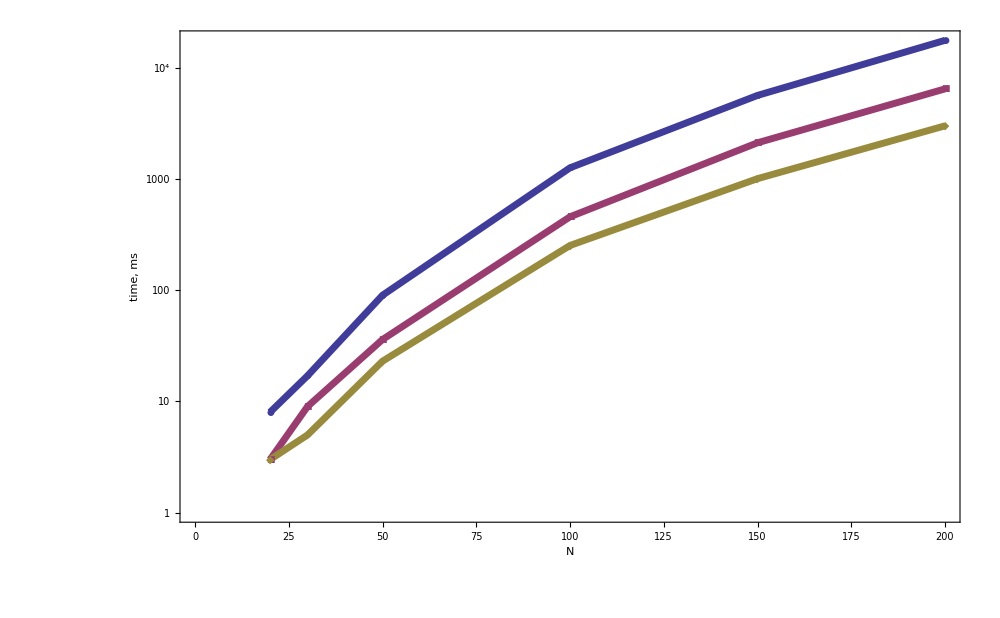

{20,30,50,100,150,200}

```mathematica
sp={8, 17, 90,1256,5618,17555};
spopress={3, 5,23,252,1004,2995};
spcond={3,9,36,456,2109,6432};
g2=ListLogPlot[{gp[NN, sp],gp[NN,spcond], gp[NN,spopress]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegendStyle->{Large},PlotLegend->{Style["SP",20,Bold],Style["SP PRECOND",20,Bold], Style["SP OPRESS",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","time, ms"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->1000]
NN//ScientificForm
```

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
10^10
```

10000000000